Here, I consider the result of mutant invasion in a cycling population with the purpose of generating a pairwise invasibility plot. This occurs when average specialist payoff exceeds average generalist payoff. First I’ll consider the outcome of  an invading alpha mutant along a cycle’s period. Below is our system of equations denoting the frequency of each strategist. We will first create expressions for the frequency of each strategist:

```mathematica
SystemNM[α_, αg_,c_,x_,u0_,v10_,v20_]:={u'[t]==(1-u[t]) u[t] (x (1-α) v1[t]-x (1-(1-α^(1/c))^c) v1[t]-x (1-α) v2[t]+x (1-(1-α^(1/c))^c) v2[t]),v1'[t]==v1[t] (x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),v2'[t]==v2[t] (x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),u[0]==u0,v1[0]==v10,v2[0]==v20,
(*Conditional statements that stores when extrema occur. This will be necessary to find the period of cycles later: *)
WhenEvent[u'[t]==0,Sow[t]],
(*We will restrict the values of the frequencies of each strategist restricted to [0,1] using conditional statements: *)
WhenEvent [EvenQ[0]&&v2[t]<0, v2[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u[t]<0, u[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0, v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u[t]>1, u[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]}
```

We will also develop expressions for the frequencies of strategists when mutants are introduced:

```mathematica
payoffs={x*(α−x),
x*(  (1-α^(1/c))^c −x),
x*(αg−x),
x*(1−α),
x*(1−(1-α^(1/c))^c),
x*(1−αg)};(*Payoffs for hosts (1 through 3)and symbionts (4 through 6)*)
```

```mathematica
{pi,pi2,pig,ψ,ψ2,ψg}=payoffs;
{pim,pi2m,pigm,ψm,ψ2m,ψgm}=payoffs/.{α-> αm}; (*Mutant Values*)
```

```mathematica
S1 = v1*ψ+v2*ψ2+(1−v1−v2)*ψg; (*Symbiont 1 *)
S2 =  v1*ψ2+v2*ψ+(1−v1−v2)*ψg; (*Symbiont 2 *)
SM1 =  v1*ψm+v2*ψ2m+(1−v1−v2)*ψg;(*Mutant Symbiont 1 *)
SM2 =  v1*ψ2m+v2*ψm+(1−v1−v2)*ψg;(*Mutant Symbiont 2 *)

Sbar = u1*S1+m1*SM1+(1-u1-m1-m2)*S2+m2*SM2 ;(*Average Symbiont Payoff*)
```

```mathematica
H1=u1*pi+ m1*pim +(1-u1-m1-m2)*pi2+m2*pi2m;(*Host 1 *)
H2 = u1*pi2+m1*pi2m+(1-u1-m1-m2)*pi+m2*pim;(*Host 2 *)
HG = pig;(*Generalist Host*)
Hbar = v1*H1+v2*H2+(1-v1-v2)*HG;(*Payoff received by a host on average*)
```

```mathematica
S1D = u1(S1-Sbar);
S2M=m2(SM2-Sbar);
(*S2D= u1(S1-Sbar);(*Symbiont 1*)*)
(*S2D =u2*(S2-Sbar);*)
SM = m1(SM1-Sbar);(*Symbiont 1*)
V1=v1(H1-Hbar);(*Host 1*)
V2=v2(H2-Hbar); (*Host 2*)
```

```mathematica
replicators={S1D,SM,S2M,V1,V2}/.{v1-> v1[t],v2-> v2[t],m1-> m1[t],m2-> m2[t], u1-> u[t]};
```

```mathematica
ClearAll[u0,v10,v20,c]
{u'[t]==replicators[[1]],m1'[t]==replicators[[2]],m2'[t]==replicators[[3]],v1'[t]==replicators[[4]],v2'[t]==replicators[[5]],u[0]==u0-m10,v1[0]==v10,m1[0]==m10,v2[0]==v20,m2[0]==m20};
```

```mathematica
SystemM2[α_,αm_,αg_,c_,x_,u0_,v10_,v20_,m10_,m20_]:={u'[t]==u[t] (x (1-α) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) v2[t]-(1-m1[t]-m2[t]-u[t]) (x (1-(1-α^(1/c))^c) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-α) v2[t])-u[t] (x (1-α) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) v2[t])-m2[t] (x (1-(1-αm^(1/c))^c) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-αm) v2[t])-m1[t] (x (1-αm) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-(1-αm^(1/c))^c) v2[t])),m1'[t]==m1[t] (x (1-αm) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-(1-αm^(1/c))^c) v2[t]-(1-m1[t]-m2[t]-u[t]) (x (1-(1-α^(1/c))^c) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-α) v2[t])-u[t] (x (1-α) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) v2[t])-m2[t] (x (1-(1-αm^(1/c))^c) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-αm) v2[t])-m1[t] (x (1-αm) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-(1-αm^(1/c))^c) v2[t])),m2'[t]==m2[t] (x (1-(1-αm^(1/c))^c) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-αm) v2[t]-(1-m1[t]-m2[t]-u[t]) (x (1-(1-α^(1/c))^c) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-α) v2[t])-u[t] (x (1-α) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) v2[t])-m2[t] (x (1-(1-αm^(1/c))^c) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-αm) v2[t])-m1[t] (x (1-αm) v1[t]+x (1-αg) (1-v1[t]-v2[t])+x (1-(1-αm^(1/c))^c) v2[t])),v1'[t]==v1[t] (x (-x+αm) m1[t]+x (-x+(1-αm^(1/c))^c) m2[t]+x (-x+(1-α^(1/c))^c) (1-m1[t]-m2[t]-u[t])+x (-x+α) u[t]-(x (-x+αm) m1[t]+x (-x+(1-αm^(1/c))^c) m2[t]+x (-x+(1-α^(1/c))^c) (1-m1[t]-m2[t]-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-v1[t]-v2[t])-(x (-x+(1-αm^(1/c))^c) m1[t]+x (-x+αm) m2[t]+x (-x+α) (1-m1[t]-m2[t]-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),v2'[t]==v2[t] (x (-x+(1-αm^(1/c))^c) m1[t]+x (-x+αm) m2[t]+x (-x+α) (1-m1[t]-m2[t]-u[t])+x (-x+(1-α^(1/c))^c) u[t]-(x (-x+αm) m1[t]+x (-x+(1-αm^(1/c))^c) m2[t]+x (-x+(1-α^(1/c))^c) (1-m1[t]-m2[t]-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-v1[t]-v2[t])-(x (-x+(1-αm^(1/c))^c) m1[t]+x (-x+αm) m2[t]+x (-x+α) (1-m1[t]-m2[t]-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),u[0]==-m10+u0,v1[0]==v10,m1[0]==m10,v2[0]==v20, m2[0]==m20,WhenEvent [EvenQ[0]&&m1[t]<0, m1[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&m2[t]<0, m2[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]<0, v2[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u[t]<0, u[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0, v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&m1[t]>1, m1[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&m2[t]>1, m2[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u[t]>1, u[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]}
```

Using these expressions, we use a function to find the rate of success of mutants following their introduction:

```mathematica
(*l and h are the maximum and minimum values of alpha that we will consider. The c term determines the shape of the trade-off function, and αg gives the alpha for the generalist host*)
SymmetricInvasionFunction[l_,h_,c_,αg_]:=
ParallelTable[{αr,αm,
(*Establish a Resident Population with arbitrary initial frequencies:*)
solution=Reap[NDSolve[SystemNM[αr,αg,c,0.5,0.25,0.28,0.24],{u,v1,v2},{t,0,10000},Method->{"StiffnessSwitching"}]];
sol=solution[[1,1]];
(*Estimate the period of the cycle resident population, and store that period as T1: *)
times=solution[[2,1]];
Drop[times,2];
T1=2*Median[Differences[times]] ,

(*Introduce mutant invaders of both symbiont 1 and 2 at each 0.1*T1 of the cycle:*)
SampleInvasion=Table[{
{uf,v1f,v2f}={u[st],v1[st],v2[st]}/.Flatten[sol];                   
				    (*[αr, 0,  0.6,1/2, 0.5,0.25,0.28,0.24, 0]*)



sol2=NDSolve[SystemM2[αr,αm,αg,c,0.5,uf,v1f,v2f,0.05,0.05],{u,m1,m2,v1,v2},{t,0,7*T1},Method->{"StiffnessSwitching"}];

{uans,m1ans,m2ans,v1ans,v2ans}= {u[t],m1[t],m2[t],v1[t],v2[t]}  /.Flatten[sol2];


(*Average mutant frequency several Periods after they invade:*)
m1avg=FindAverage[m1ans,4*T1,7*T1];
(*Average frequency of symbiont 1: *)
uavg=FindAverage[uans,4*T1,7*T1];
(*Compare the frequency of symbiont 1 and the symbiont 1 mutant: *)
If[m1avg>uavg,1,0],
(*If mutant average frequency has increased from its initial low frequency, we deem this a successful invasion*)
If[m1avg>0.05,1,0],
(*Also give the frequency of the mutant after invasion: *)
m1avg}
,
{st,5000,5000+T1,0.01*T1}];

(*Determine if on average the mutants successfully Invade:*)

AvgResult=Mean[Take[Flatten[SampleInvasion],{3,-1,3}]],
Mean[Take[Flatten[SampleInvasion],{2,-1,3}]],
Mean[Take[Flatten[SampleInvasion],{1,-1,3}]]
(*This is the average frequency with which the mutant successfully invaded: *)
(*Finally, this is a bindary definition of successful invasion: *)
},
{αr,l,h,0.01},{αm,l,h,0.01}];
```

Now, we’ll use this function to find the symbiont PIP for the concave down, linear and concave up PIP’s:

```mathematica
CCSSYM=SymmetricInvasionFunction[0.23,0.97,1/2,0.6];
```

```mathematica
ListDensityPlot[Flatten[CCSSYM,1][[All,{1,2,5}]],PlotLegends->Automatic,  FrameLabel->{"α_r","α_m"},(*Scale color function from 0 to 1: *)ColorFunction->"M10DefaultDensityGradient", ColorFunction->(ColorData["M10DefaultDensityGradient"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False]
```

Next the linear case:

```mathematica
LINSSYM=SymmetricInvasionFunction[0.51,0.99,1,0.3];
```

```mathematica
ListDensityPlot[Flatten[LINSSYM,1][[All,{1,2,5}]],PlotLegends->Automatic,  FrameLabel->{"α_r","α_m"},ColorFunction->"M10DefaultDensityGradient", ColorFunction->(ColorData["M10DefaultDensityGradient"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False]
```

Finally the concave up (i.e. concave) case:

```mathematica
CVSSYM=SymmetricInvasionFunction[0.55,0.99,2,0.3];
```

```mathematica
ListDensityPlot[Flatten[CVSSYM,1][[All,{1,2,4}]],PlotLegends->Automatic,  FrameLabel->{"α_r","α_m"},ColorFunction->"M10DefaultDensityGradient", ColorFunction->(ColorData["M10DefaultDensityGradient"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False]
```

Now with symbionts complete we’ll consider the outcome with invading hosts. First we construct new expressions for the frequency of mutant hosts with new values of alpha:

```mathematica
payoffs={x*(α−x),
x*(  (1-α^(1/c))^c −x),
x*(αg−x),
x*(1−α),
x*(1−(1-α^(1/c))^c),
x*(1−αg)};(*Payoffs for hosts (1 through 3)and symbionts (4 through 6)*)
```

```mathematica
{pi,pi2,pig,ψ,ψ2,ψg}=payoffs;
{pim,pi2m,pigm,ψm,ψ2m,ψgm}=payoffs/.{α-> αm}; (*Mutant Values*)
```

```mathematica
S1 = v1*ψ+m1*ψm+v2*ψ2+m2*ψ2m+(1−v1−v2-m1-m2)*ψg; (*Symbiont 1 *)
S2 = v1*ψ2+m1*ψ2m+v2*ψ+m2*ψm+(1−v1−v2-m1-m2)*ψg; (*Symbiont 2 *)

Sbar = u*S1+(1-u)*S2 ;(*Average Symbiont Payoff*)
```

```mathematica
H1=u*pi+(1-u)*pi2;(*Host 1 *)
H1M = u*pim+(1-u)*pi2m;(*Host 1 Mutant*)
H2 = u*pi2+(1-u)*pi;(*Host 2 *)
H2M = u*pi2m+(1-u)*pim;(*Host 2 *)
HG = pig;(*Generalist Host*)
Hbar = v1*H1+m1*H1M+v2*H2+m2*H2M+(1-v1-v2-m1-m2)*HG;(*Payoff received by a host on average*)
```

```mathematica
S1D = u(S1-Sbar);
V1=v1(H1-Hbar);(*Host 1*)
V2=v2(H2-Hbar); (*Host 2*)
M1 = m1(H1M-Hbar); (*Host 1 Mutant*)
M2=m2(H2M-Hbar); (*Host 2 Mutant*)
```

```mathematica
replicators={S1D,V1,M1,V2,M2}/.{v1-> v1[t],v2-> v2[t],m1-> m1[t],m2-> m2[t], u-> u[t]};
```

```mathematica
{u'[t]==replicators[[1]],v1'[t]==replicators[[2]],v1'[t]==replicators[[3]],v2'[t]==replicators[[4]],m2'[t]==replicators[[5]],u[0]==u0,v1[0]==v10-m10,m1[0]==m10,v2[0]==v20-m20,m2[0]==m20};
```

```mathematica
(*Here is our system with 2 host mutants: *)
SystemHM[α_,αm_,αg_,c_,x_,u0_,v10_,v20_,m10_,m20_]:=
{u'[t]==u[t] (x (1-αm) m1[t]+x (1-(1-αm^(1/c))^c) m2[t]+x (1-α) v1[t]+x (1-αg) (1-m1[t]-m2[t]-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) v2[t]-(1-u[t]) (x (1-(1-αm^(1/c))^c) m1[t]+x (1-αm) m2[t]+x (1-(1-α^(1/c))^c) v1[t]+x (1-αg) (1-m1[t]-m2[t]-v1[t]-v2[t])+x (1-α) v2[t])-u[t] (x (1-αm) m1[t]+x (1-(1-αm^(1/c))^c) m2[t]+x (1-α) v1[t]+x (1-αg) (1-m1[t]-m2[t]-v1[t]-v2[t])+x (1-(1-α^(1/c))^c) v2[t])),v1'[t]==v1[t] (x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-m2[t] (x (-x+αm) (1-u[t])+x (-x+(1-αm^(1/c))^c) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),v1'[t]==m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t]-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-m2[t] (x (-x+αm) (1-u[t])+x (-x+(1-αm^(1/c))^c) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),v2'[t]==v2[t] (x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-m2[t] (x (-x+αm) (1-u[t])+x (-x+(1-αm^(1/c))^c) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),m2'[t]==m2[t] (x (-x+αm) (1-u[t])+x (-x+(1-αm^(1/c))^c) u[t]-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-m2[t] (x (-x+αm) (1-u[t])+x (-x+(1-αm^(1/c))^c) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),u[0]==u0,v1[0]==-m10+v10,m1[0]==m10,v2[0]==-m20+v20,m2[0]==m20,WhenEvent [EvenQ[0]&&m1[t]<0, m1[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&m2[t]<0, m2[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]<0, v2[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u[t]<0, u[t]-> 0,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]<0, v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&m1[t]>1, m1[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&m2[t]>1, m2[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u[t]>1, u[t]-> 1,"LocationMethod"->"LinearInterpolation"],
WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]}
```

Now a function to systematically consider host invasion:

```mathematica
HostInvasionFunction[l_,h_,c_,αg_]:=
ParallelTable[{αr,αm,
(*Establish a Resident Population with arbitrary initial frequencies:*)
solution=Reap[NDSolve[SystemNM[αr,αg,c,0.5,0.25,0.28,0.24],{u,v1,v2},{t,0,10000},Method->{"StiffnessSwitching"}]];
sol=solution[[1,1]];

times=solution[[2,1]];
Drop[times,2];
T1=2*Median[Differences[times]] ,

(*Introduce mutant invaders at each 0.1*T1 of the cycle:*)
SampleInvasion=Table[{
{uf,v1f,v2f}={u[st],v1[st],v2[st]}/.Flatten[sol];                   
				    (*[αr, 0,  0.6,1/2, 0.5,0.25,0.28,0.24, 0]*)



sol2=NDSolve[SystemM2[αr,αm,αg,c,0.5,uf,v1f,v2f,0.05,0.05],{u,m1,m2,v1,v2},{t,0,7*T1},Method->{"StiffnessSwitching"}];

{uans,m1ans,m2ans,v1ans,v2ans}= {u[t],m1[t],m2[t],v1[t],v2[t]}  /.Flatten[sol2];


(*Average mutant frequency several Periods after they invade:*)
m1avg=FindAverage[m1ans,4*T1,7*T1];
v1avg=FindAverage[v1ans,4*T1,7*T1];
If[m1avg>v1ans,1,0],
If[m1avg>0.05,1,0],
m1avg(*If mutant average frequency has increased from its initial low frequency, we deem this a successful invasion*)
}
,
{st,5000,5000+T1,0.01*T1}];

(*Determine if on average the mutants successfully Invade:*)

AvgResult=Mean[Take[Flatten[SampleInvasion],{3,-1,3}]],
Mean[Take[Flatten[SampleInvasion],{2,-1,3}]],
Mean[Take[Flatten[SampleInvasion],{1,-1,3}]]
(*This is the average frequency with which the mutant successfully invaded: *)
(*Finally, this is a bindary definition of successful invasion: *)
},
{αr,l,h,0.01},{αm,l,h,0.01}];
```

Now we’ll use this function for each of our trade-off functions, beginning with the concave down trade-off:

```mathematica
CCHSYM=HostInvasionFunction[0.23,0.97,1/2,0.6];
```

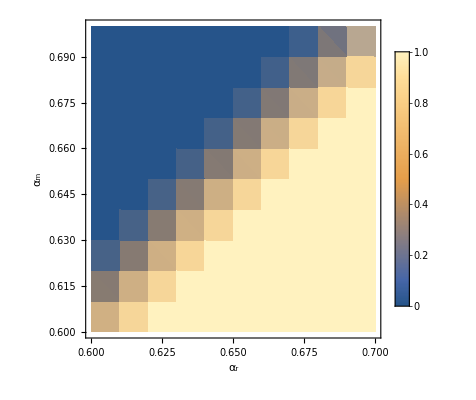

```mathematica
ListDensityPlot[Flatten[CCHSYM,1][[All,{1,2,5}]],PlotLegends->Automatic,  FrameLabel->{"α_r","α_m"},(*Scale color function from 0 to 1: *)ColorFunction->"M10DefaultDensityGradient", ColorFunction->(ColorData["M10DefaultDensityGradient"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False]
```

Next the linear trade-off:

```mathematica
LHSYM=HostInvasionFunction[0.51,0.99,1,0.3];
```

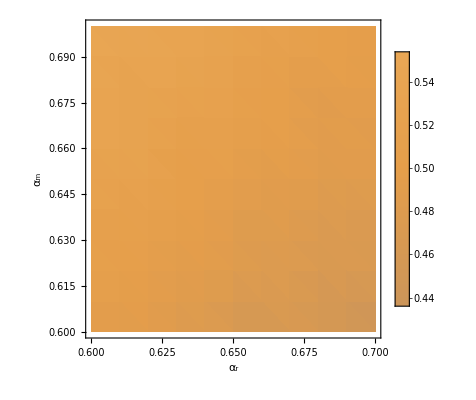

```mathematica
ListDensityPlot[Flatten[LHSYM,1][[All,{1,2,5}]],PlotLegends->Automatic,  FrameLabel->{"α_r","α_m"},(*Scale color function from 0 to 1: *)ColorFunction->"M10DefaultDensityGradient", ColorFunction->(ColorData["M10DefaultDensityGradient"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False]
```

Finally the concave up trade-off function:

```mathematica
CVHSYM=HostInvasionFunction[0.55,0.97,2,0.3];
```

```mathematica
ListDensityPlot[Flatten[CVHSYM,1][[All,{1,2,5}]],PlotLegends->Automatic,  FrameLabel->{"α_r","α_m"},(*Scale color function from 0 to 1: *)ColorFunction->"M10DefaultDensityGradient", ColorFunction->(ColorData["M10DefaultDensityGradient"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False]
```